## Fidelidad vs pureza de Choi

```mathematica
Get["~/Documents/chaos_meets_channels/Mathematica_packages/QMB.wl"]
```

```mathematica
hx=1.;
hz=0.5;
J=1.;
L=6;
```

```mathematica
kraus=1/2*Pauli[Join[{#},ConstantArray[0,L-1]]]&/@Range[0,3];
(* Completeness relation *)
Total[#.ConjugateTranspose[#]&/@kraus];
```

------------------

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
U[t_]:=MatrixExp[-I*H*t]
ψ=RandomChainProductState[L-1];
```

```mathematica
ϕ=IdentityMatrix[2];
```

```mathematica
ClearAll[ρ,ℰ];
ρ[t_]:=Chop[U[t].KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]].ConjugateTranspose[U[t]]]
ℰ[ρ_]:=Total[#.ρ.ConjugateTranspose[#]&/@kraus]
ChoiPurity[t_]:=Chop[Purity[MatrixPartialTrace[ρ[t],1,{2,4}]]]
```

```mathematica
ClearAll[α];
α[i_,j_,t_]:=Chop@Braket[Flatten[KroneckerProduct[ϕ[[i+1]],ψ]],ConjugateTranspose[U[t]].ℰ[ρ[t]].U[t].Flatten[KroneckerProduct[ϕ[[j+1]],ψ]]]
```

```mathematica
fidelity=fidelitynum=purity={};
Table[
(* Fidelity *)
F=Chop[Tr[MatrixPower[MatrixPower[ρ[t],1/2].ℰ[ρ[t]].MatrixPower[ρ[t],1/2],1/2]]^2];
Fnum=1/2(α[0,0,t]+α[1,1,t]+2Sqrt[α[0,0,t]*α[1,1,t]-Abs[α[0,1,t]]^2]);

(* Pureza de Choi *)
P=Chop[Purity[MatrixPartialTrace[ρ[t],1,{2,2^(L-1)}]]];

Round[F,10.^-6]==Round[P,10.^-6];
AppendTo[fidelitynum,{t,Fnum}];
AppendTo[fidelity,{t,F}];
AppendTo[purity,{t,P}];
,{t,0,30,0.05}];
```

```mathematica
t=200;{fidelity[[t]],fidelitynum[[t]],purity[[t]]}
```

{{9.95,0.643312},{9.95,0.643312},{9.95,0.643355}}

```mathematica
t=3.05;
α[0,0,t]+α[1,1,t]
2*Sqrt[α[0,0,t]*α[1,1,t]-Abs[α[0,1,t]]^2]
α[0,0,t]*α[1,1,t]
α[0,0,t]^2
Abs[α[0,1,t]]^2
```

0.929619

0.929611

0.216047

0.216913

3.05857×10^-6

```mathematica
t=104.51;σ=Chop[ℰ[ρ[t]]];
```

```mathematica
MatrixPartialTrace[σ,2,{2,2^(L-1)}]
```

{{0.5,0},{0,0.5}}

```mathematica
σ//Eigenvalues//Chop
```

{0.287486,0.287486,0.209414,0.209414,0.00247894,0.00247894,0.000621281,0.000621281,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
{eigvals,eigvecs}=Chop[Eigensystem[σ]];
```

```mathematica
Total[eigvals[[#]]*MatrixPartialTrace[Dyad[eigvecs[[#]]],2,{2,2^(L-1)}]&/@Range[8]]
```

{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.5+0. ⅈ}}

```mathematica
σ//Eigenvalues//Chop
```

{0.287486,0.287486,0.209414,0.209414,0.00247894,0.00247894,0.000621281,0.000621281,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Chop[MatrixPartialTrace[Dyad[eigvecs[[#]]],2,{2,2^(L-1)}]]&/@Range[8]
```

{{{1.,0},{0,0}},{{0,0},{0,1.}},{{1.,0},{0,0}},{{0,0},{0,1.}},{{1.,0},{0,0}},{{0,0},{0,1.}},{{1.,0},{0,0}},{{0,0},{0,1.}}}

```mathematica
β=Chop[MatrixPartialTrace[Dyad[eigvecs[[#]]],1,{2,2^(L-1)}]]&/@Range[1,8,2]
```

```mathematica
β[[4]]//Eigenvalues//Chop
```

{1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Flatten[KroneckerProduct[ϕ[[i+1]],Conjugate[ψ]]].ConjugateTranspose[U[t]].σ.U[t].Flatten[KroneckerProduct[ϕ[[j+1]],ψ]],{i,0,1},{j,0,1}]//Chop//MatrixForm
```

(0.2554 | -0.000546762-0.00183242 ⅈ
-0.000546762+0.00183242 ⅈ | 0.250635)

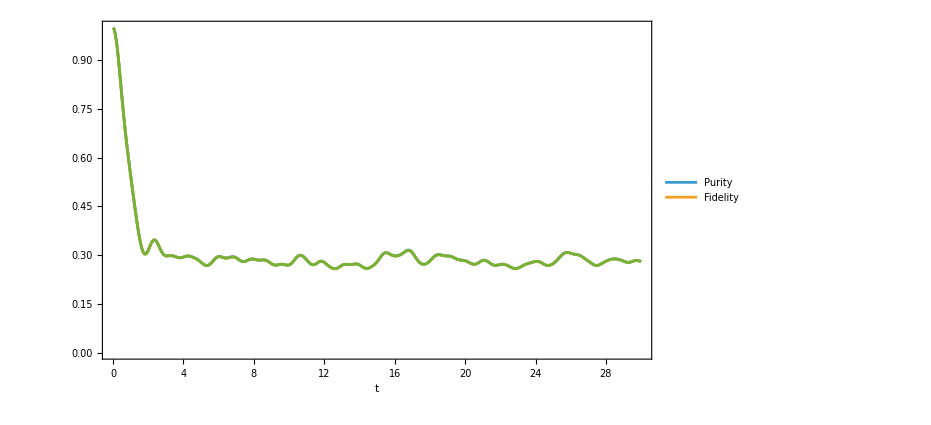

```mathematica
ListPlot[{purity,fidelity,fidelitynum},
Joined->True,
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{TraditionalForm[HoldForm[t]], Nothing},
PlotLegends->Placed[{"Purity","Fidelity"},{Right,Top}],
LabelStyle->Directive[Black,FontSize->22],
ImageSize->500
]
```

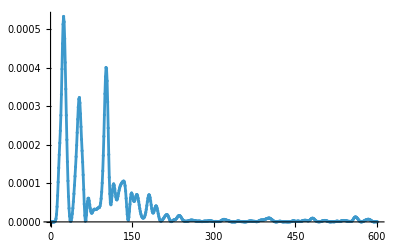

```mathematica
ListPlot[Chop[purity[[All,2]]-fidelitynum[[All,2]]],
Joined->True,
Mesh->All,
PlotRange->Full
]
```

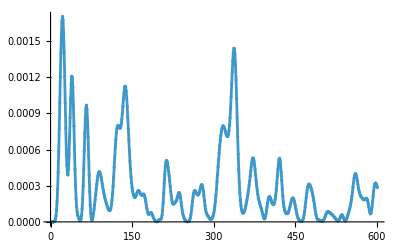

```mathematica
ListPlot[Chop[purity[[All,2]]-fidelitynum[[All,2]]],
Joined->True,
Mesh->All,
PlotRange->Full
]
```

------

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
U[t_]:=MatrixExp[-I*H*t]
ψ=RandomChainProductState[L-1];
```

```mathematica
fidelity=fidelitynum=purity={};
Table[
ρ=Chop[#.KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]].ConjugateTranspose[#]&[U[t]]];
ℰρ=Total[#.ρ.ConjugateTranspose[#]&/@kraus];

(* Fidelity *)
F=Chop[Tr[MatrixPower[MatrixPower[ρ,1/2].ℰρ.MatrixPower[ρ,1/2],1/2]]^2];
Fnum=1/2(α[0,0,t]+α[1,1,t]+2Sqrt[α[0,0,t]*α[1,1,t]-Abs[α[0,1,t]]^2]);

(* Pureza de Choi *)
P=Chop[Purity[MatrixPartialTrace[ρ,1,{2,2^(L-1)}]]];

Round[F,10.^-6]==Round[P,10.^-6];
AppendTo[fidelitynum,{t,Fnum}];
AppendTo[fidelity,{t,F}];
AppendTo[purity,{t,P}];
,{t,0,10,0.05}];
```

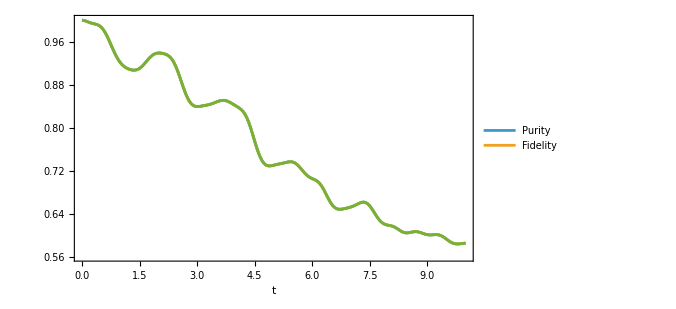

```mathematica
ListPlot[{purity,fidelity,fidelitynum},
Joined->True,
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{TraditionalForm[HoldForm[t]], Nothing},
PlotLegends->Placed[{"Purity","Fidelity"},{Right,Top}],
LabelStyle->Directive[Black,FontSize->22],
ImageSize->500
]
```

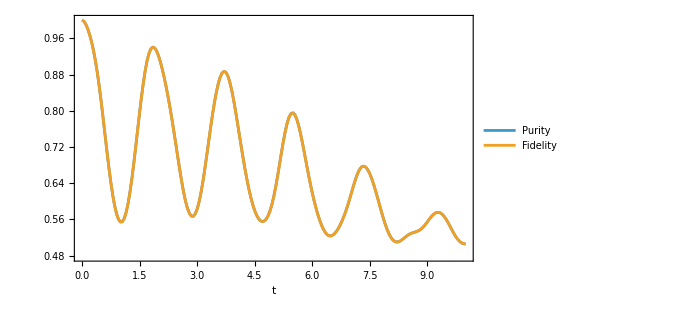

```mathematica
ListPlot[{purity,fidelity},
Joined->True,
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{TraditionalForm[HoldForm[t]], Nothing},
PlotLegends->Placed[{"Purity","Fidelity"},{Right,Top}],
LabelStyle->Directive[Black,FontSize->22],
ImageSize->500
]
```

```mathematica
purity[[-3]]
```

{9.9,0.545922}

```mathematica
fidelity[[-3]]
```

{9.9,0.545904}

```mathematica
t=9.9;1/2(α[0,0,t]+α[1,1,t]+2Sqrt[α[0,0,t]*α[1,1,t]-Abs[α[0,1,t]]^2])
```

0.556667

### XXZ

```mathematica
?LeaSpinChainHamiltonian
```

```mathematica
L=7;
d=3;
Jxy=5.;Jz=1;
ϵd=0.1;ω=0;
```

```mathematica
kraus=1/2*Pauli[Join[{#},ConstantArray[0,L-1]]]&/@Range[0,3];
(* Completeness relation *)
Total[#.ConjugateTranspose[#]&/@kraus]//MatrixForm;
```

```mathematica
H=LeaSpinChainHamiltonian[Jxy,Jz,ω,ϵd,L,d];
U[t_]:=MatrixExp[-I*H*t]
ψ=RandomChainProductState[L-1];

fidelity=fidelitynum=purity={};
Table[
(* Fidelity *)
F=Chop[Tr[MatrixPower[MatrixPower[ρ[t],1/2].ℰ[ρ[t]].MatrixPower[ρ[t],1/2],1/2]]^2];
Fnum=1/2(α[0,0,t]+α[1,1,t]+2Sqrt[α[0,0,t]*α[1,1,t]-Abs[α[0,1,t]]^2]);

(* Pureza de Choi *)
P=Chop[Purity[MatrixPartialTrace[ρ[t],1,{2,2^(L-1)}]]];

Round[F,10.^-6]==Round[P,10.^-6];
AppendTo[fidelitynum,{t,Fnum}];
AppendTo[fidelity,{t,F}];
AppendTo[purity,{t,P}];
,{t,0,30,0.1}];
```

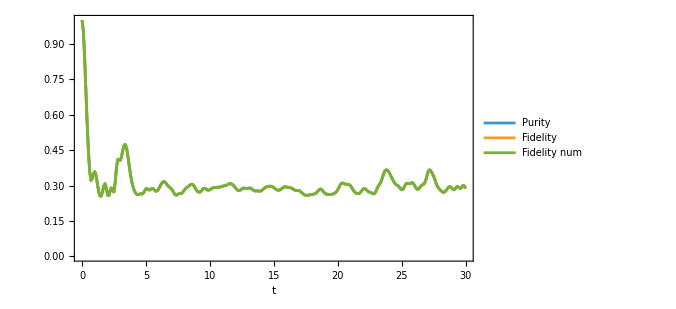

```mathematica
ListPlot[{purity,fidelity,fidelitynum},
Joined->True,
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{TraditionalForm[HoldForm[t]], Nothing},
PlotLegends->Placed[{"Purity","Fidelity","Fidelity num"},{Right,Top}],
LabelStyle->Directive[Black,FontSize->22],
ImageSize->500
]
```

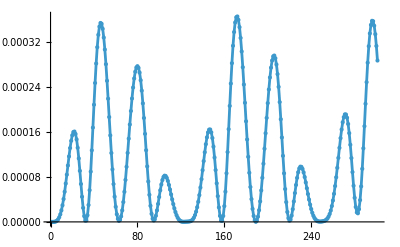

```mathematica
(*L=7;
d=3;
Jxy=0.1;Jz=1;
ϵd=0.3;ω=0;*)
ListPlot[Chop[purity[[All,2]]-fidelitynum[[All,2]]],
Joined->True,
Mesh->All,
PlotRange->Full
]
```

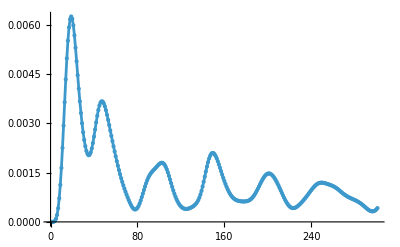

```mathematica
(*L=7;
d=3;
Jxy=1.;Jz=1;
ϵd=1.;ω=0;*)
ListPlot[Chop[purity[[All,2]]-fidelitynum[[All,2]]],
Joined->True,
Mesh->All,
PlotRange->Full
]
```

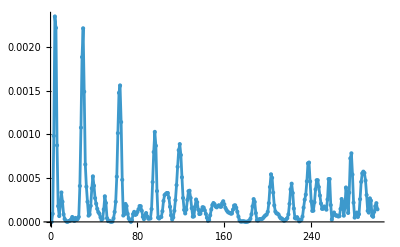

```mathematica
(*L=7;
d=3;
Jxy=5.;Jz=1;
ϵd=0.1;ω=0;*)
ListPlot[Chop[purity[[All,2]]-fidelitynum[[All,2]]],
Joined->True,
Mesh->All,
PlotRange->Full
]
```

## Analítica Fidelidad

```mathematica
Get["~/Documents/chaos_meets_channels/Mathematica_packages/QMB.wl"]
```

```mathematica
Get["~/Documents/chaos_meets_channels/Mathematica_packages/Chaometer.wl"]
```

```mathematica
hx=1.;
hz=0.5;
J=1.;
L=3;
```

```mathematica
kraus=1/2*Pauli[Join[{#},ConstantArray[0,L-1]]]&/@Range[0,3];

(* Completeness relation *)
Total[#.ConjugateTranspose[#]&/@kraus]==IdentityMatrix[2^L]
```

True

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
U[t_]:=MatrixExp[-I*H*t]
ψ=RandomChainProductState[L-1];

t=0.;u=U[t];
ρ=Chop[u.KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]].ConjugateTranspose[u]];
ℰρ=Total[#.ρ.ConjugateTranspose[#]&/@kraus];
```

```mathematica
ϕ=IdentityMatrix[2];
```

### Eigenvalores de√(ρ_SE(t)) ✓

```mathematica
Chop[MatrixPower[ρ,1/2]]//Eigenvalues//Chop
```

{0.707107,0.707107,0,0,0,0,0,0}

```mathematica
(1/√2)*Chop[u.KroneckerProduct[{{1,0},{0,0}},Dyad[ψ]].ConjugateTranspose[u]+u.KroneckerProduct[{{0,0},{0,1}},Dyad[ψ]].ConjugateTranspose[u]]//Eigenvalues//Chop
```

{0.707107,0.707107,0,0,0,0,0,0}

### Eigenvalores de√(ρ_SE(t))ℰ(ρ_SE(t))√(ρ_SE(t)) ✓

```mathematica
MatrixPower[ρ,1/2].ℰρ.MatrixPower[ρ,1/2]//Eigenvalues//Chop
```

{0.132577,0.0942929,0,0,0,0,0,0}

```mathematica
α[i_,j_]:=Chop[Braket[Flatten[KroneckerProduct[ϕ[[i+1]],ψ]],ConjugateTranspose[u].ℰρ.u.Flatten[KroneckerProduct[ϕ[[j+1]],ψ]]]]
```

```mathematica
(1/4)*(α[0,0]+α[1,1]+Sqrt[(α[0,0]-α[1,1])^2+4Abs[α[0,1]]^2])

(1/4)*(α[0,0]+α[1,1]-Sqrt[(α[0,0]-α[1,1])^2+4Abs[α[0,1]]^2])
```

0.25

0.25

### Eigenvalores de√(√(ρ_SE(t))ℰ(ρ_SE(t))√(ρ_SE(t))) ✓

```mathematica
MatrixPower[MatrixPower[ρ,1/2].ℰρ.MatrixPower[ρ,1/2],1/2]//Eigenvalues//Chop
```

{0.35562,0.315446,0,0,0,0,0,0}

```mathematica
Sqrt[(1/4)*(α[0,0]+α[1,1]+Sqrt[(α[0,0]-α[1,1])^2+4Abs[α[0,1]]^2])]

Sqrt[(1/4)*(α[0,0]+α[1,1]-Sqrt[(α[0,0]-α[1,1])^2+4Abs[α[0,1]]^2])]
```

0.35562

0.315446

### Tr(√(√(ρ_SE(t))ℰ(ρ_SE(t))√(ρ_SE(t)))) ✓

```mathematica
Chop[Tr[MatrixPower[MatrixPower[ρ,1/2].ℰρ.MatrixPower[ρ,1/2],1/2]]]
```

0.671066

```mathematica
Sqrt[(1/4)*(α[0,0]+α[1,1]+Sqrt[(α[0,0]-α[1,1])^2+4Abs[α[0,1]]^2])]+Sqrt[(1/4)*(α[0,0]+α[1,1]-Sqrt[(α[0,0]-α[1,1])^2+4Abs[α[0,1]]^2])]
```

0.671066

### Fidelidad ✓

```mathematica
Chop[Tr[MatrixPower[MatrixPower[ρ,1/2].ℰρ.MatrixPower[ρ,1/2],1/2]]^2]
```

1.

```mathematica
(* Con los eigenvalores *)
1/2*((α[0,0]+α[1,1]+2*Sqrt[α[0,0]*α[1,1]-Abs[α[0,1]]^2]))
```

1.

```mathematica
1/2*(α[0,0]+α[1,1])
```

0.5

```mathematica
Sqrt[α[0,0]*α[1,1]-Abs[α[0,1]]^2]
```

0.5

### Otros

```mathematica
(* Choi purity *)
A=KroneckerProduct[IdentityMatrix[2^(L-1)],Dyad[ψ]];
Chop[Purity[1/2*ChoiMatrix[u,A,L]]]
```

1.

```mathematica
(α[0,0]+α[1,1])
```

1.

## Fidelidad entre Tr(ρ_SE(t)) y Tr(ℰ[ρ_SE(t)])

```mathematica
Get["~/Documents/chaos_meets_channels/Mathematica_packages/QMB.wl"]
Get["~/Documents/chaos_meets_channels/Mathematica_packages/Chaometer.wl"]
```

```mathematica
Fidelity[ρ_,σ_]:=Chop[Tr[MatrixPower[MatrixPower[ρ,1/2].σ.MatrixPower[ρ,1/2],1/2]]^2]
```

```mathematica
hx=1.;
hz=0.5;
J=1.;
L=6;
```

```mathematica
(* Operadores de Kraus de canal completamente depolarizante *)
kraus=1/2*Pauli[Join[{#},ConstantArray[0,L-1]]]&/@Range[0,3];

(* Completeness relation *)
Total[#.ConjugateTranspose[#]&/@kraus]==IdentityMatrix[2^L]
```

True

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
U[t_]:=MatrixExp[-I*H*t]
ψ=RandomChainProductState[L-1];
```

```mathematica
ϕ=IdentityMatrix[2];
```

```mathematica
ClearAll[ρ,ℰ];
ρ[t_]:=Chop[U[t].KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]].ConjugateTranspose[U[t]]]
ℰ[ρ_]:=Total[#.ρ.ConjugateTranspose[#]&/@kraus]
ChoiPurity[t_]:=Chop[Purity[MatrixPartialTrace[ρ[t],1,{2,4}]]]
```

```mathematica
{i,j}={0,1};t=10.1;
ClearAll[α];
α[i_,j_,t_]:=Chop@Braket[Flatten[KroneckerProduct[ϕ[[i+1]],ψ]],ConjugateTranspose[U[t]].ℰ[ρ[t]].U[t].Flatten[KroneckerProduct[ϕ[[j+1]],ψ]]]
```

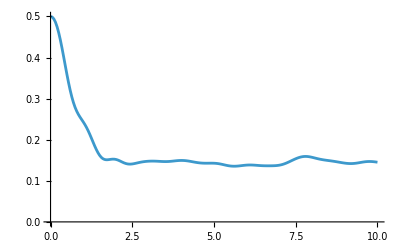

```mathematica
ListPlot[Table[
t=i;
{t,Sqrt[α[0,0,t]*α[1,1,t]-Abs[α[0,1,t]]^2]}
,{i,0,10,0.05}],
Joined->True,
PlotRange->All
]
```

## Recycle bin

```mathematica
-1/2(PauliMatrix[0]-PauliMatrix[1])+I*1/2(PauliMatrix[0]-PauliMatrix[2])+(1-I)/2*PauliMatrix[0]//MatrixForm
```

(0 | 0
1 | 0)

```mathematica
-Outer[Times,#,#]&[{1,-1}]+I* Outer[Times,#,Conjugate[#]]&[{1,-I}]+(1-I)IdentityMatrix[2]//MatrixForm
```

(0 | 0
2 | 0)

```mathematica
(1+I)(1-I)
```

2

```mathematica
MatrixForm[ρ=Outer[Times,Conjugate[#],#]&[Normalize[{1,0,0,1}]]]
```

(1/2 | 0 | 0 | 1/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 0 | 0 | 1/2)

```mathematica
MatrixForm[ρ2=Outer[Times,Conjugate[#],#]&[Normalize[{1,0,0,0,0,0,0,1}]]]
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2)

```mathematica
kraus=1/2KroneckerProduct[PauliMatrix[#],PauliMatrix[0]]&/@{0,1,2,3};
Total[#.ConjugateTranspose[#]&/@kraus]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
kraus2=1/2KroneckerProduct[PauliMatrix[#],PauliMatrix[0],PauliMatrix[0]]&/@{0,1,2,3};
Total[#.ConjugateTranspose[#]&/@kraus2]
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Total[#.ρ.ConjugateTranspose[#]&/@kraus]//MatrixForm
```

(1/4 | 0 | 0 | 0
0 | 1/4 | 0 | 0
0 | 0 | 1/4 | 0
0 | 0 | 0 | 1/4)

```mathematica
Total[#.ρ2.ConjugateTranspose[#]&/@kraus2]//MatrixForm
```

(1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4)

```mathematica
U=1/√2{{1,0,0,1},{0,1,1,0},{0,1,-1,0},{1,0,0,-1}}
```

{{1/(√2),0,0,1/(√2)},{0,1/(√2),1/(√2),0},{0,1/(√2),-1/(√2),0},{1/(√2),0,0,-1/(√2)}}

```mathematica
MatrixPartialTrace[U.Outer[Times,#,#]&[Flatten[KroneckerProduct[{1,0},{1,0}]]].ConjugateTranspose[U],2,2]
```

{{1/2,0},{0,1/2}}

```mathematica
MatrixPartialTrace[U.KroneckerProduct[{{1/2,0},{0,1/2}},{{1,0},{0,0}}].ConjugateTranspose[U],1,2]
```

{{1/2,0},{0,1/2}}

```mathematica
σ=U.KroneckerProduct[{{1/2,0},{0,1/2}},{{1,0},{0,0}}].ConjugateTranspose[U]
```

{{1/4,0,0,1/4},{0,1/4,-1/4,0},{0,-1/4,1/4,0},{1/4,0,0,1/4}}

```mathematica
Tr[σ.σ]
```

1/2

```mathematica
Tr[σ]
```

1

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"]
```

```mathematica
?MatrixPartialTrace
```

```mathematica
FullSimplify[Eigenvalues[{{a,b},{Conjugate[b],c}}]]/.{a->p ψ11,b->√(p(1-p)ψ12),c->(1-p)ψ22}
```

{1/2 (p ψ11+(1-p) ψ22-√((p ψ11-(1-p) ψ22)^2+4 √((1-p) p ψ12) Conjugate[√((1-p) p ψ12)])),1/2 (p ψ11+(1-p) ψ22+√((p ψ11-(1-p) ψ22)^2+4 √((1-p) p ψ12) Conjugate[√((1-p) p ψ12)]))}

```mathematica
Expand[Total[Sqrt[Eigenvalues[{{a,b},{Conjugate[b],c}}]]]^2]//FullSimplify
```

a+c+√(a+c-√((a-c)^2+4 b Conjugate[b])) √(a+c+√((a-c)^2+4 b Conjugate[b]))

```mathematica
(a+c-√((a-c)^2+4 b Conjugate[b]))(a+c+√((a-c)^2+4 b Conjugate[b]))//FullSimplify
```

4 a c-4 b Conjugate[b]

```mathematica
FullSimplify[Eigenvalues[{{a,b},{Conjugate[b],c}}]]
Sqrt[FullSimplify[Eigenvalues[{{a,b},{Conjugate[b],c}}]]]
Total[Sqrt[FullSimplify[Eigenvalues[{{a,b},{Conjugate[b],c}}]]]]^2//FullSimplify
```

{1/2 (a+c-√((a-c)^2+4 b Conjugate[b])),1/2 (a+c+√((a-c)^2+4 b Conjugate[b]))}

{(√(a+c-√((a-c)^2+4 b Conjugate[b])))/(√2),(√(a+c+√((a-c)^2+4 b Conjugate[b])))/(√2)}

a+c+√(a+c-√((a-c)^2+4 b Conjugate[b])) √(a+c+√((a-c)^2+4 b Conjugate[b]))

```mathematica
FullSimplify[Expand[(a+c-√((a-c)^2+4 b Conjugate[b]))(a+c+√((a-c)^2+4 b Conjugate[b]))]]
```

4 a c-4 b Conjugate[b]

```mathematica
Total[Sqrt[Eigenvalues[1/2{{ℰ00,ℰ01},{Conjugate[ℰ01],ℰ11}}]]]^2//Expand//FullSimplify
```

1/2 (ℰ00+ℰ11+√(ℰ00+ℰ11-√((ℰ00-ℰ11)^2+4 ℰ01 Conjugate[ℰ01])) √(ℰ00+ℰ11+√((ℰ00-ℰ11)^2+4 ℰ01 Conjugate[ℰ01])))

```mathematica
√((ℰ00+ℰ11-√((ℰ00-ℰ11)^2+4 ℰ01 Conjugate[ℰ01]))(ℰ00+ℰ11+√((ℰ00-ℰ11)^2+4 ℰ01 Conjugate[ℰ01])))//Expand//Simplify
```

2 √(ℰ00 ℰ11-ℰ01 Conjugate[ℰ01])

```mathematica
ρ=Chop[#.KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]].ConjugateTranspose[#]&[U[1.2]]];
```

```mathematica
kraus=1/2{Pauli[{0,0,0}],Pauli[{1,0,0}],Pauli[{2,0,0}],Pauli[{3,0,0}]}
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
ℰρ=Total[#.ρ.ConjugateTranspose[#]&/@kraus];
MatrixForm[MatrixPartialTrace[ℰρ,2,{2,4}]]
```

(0.5+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.5+0. ⅈ)

```mathematica
Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{1,0},ψ]]//Chop

Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{0,1},ψ]]//Chop

Flatten[KroneckerProduct[{0,1},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{1,0},ψ]]//Chop

Flatten[KroneckerProduct[{0,1},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{0,1},ψ]]//Chop
```

0.213448

0.000937438-0.00803888 ⅈ

0.000937438+0.00803888 ⅈ

0.277477

```mathematica
Abs[Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{0,1},ψ]]]^2
```

0.0000655023

```mathematica
(Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{1,0},ψ]])*(Flatten[KroneckerProduct[{0,1},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[1.2]].Flatten[KroneckerProduct[{0,1},ψ]])//Chop
```

0.0592269

```mathematica
t=0.;
ρ=Chop[#.KroneckerProduct[IdentityMatrix[2]/2,Dyad[ψ]].ConjugateTranspose[#]&[U[t]]];
Chop@Purity[MatrixPartialTrace[ρ,1,{2,4}]]
```

1.

```mathematica
t=0.;u=U[t];

Chop[
1/2*(Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[t]].Flatten[KroneckerProduct[{1,0},ψ]]+Flatten[KroneckerProduct[{0,1},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[t]].Flatten[KroneckerProduct[{0,1},ψ]]+2Sqrt[(Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[t]].Flatten[KroneckerProduct[{1,0},ψ]])*(Flatten[KroneckerProduct[{0,1},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[t]].Flatten[KroneckerProduct[{0,1},ψ]])-Abs[Flatten[KroneckerProduct[{1,0},Conjugate[ψ]]].ConjugateTranspose[#].ℰρ.#&[U[t]].Flatten[KroneckerProduct[{0,1},ψ]]]^2])]
```

0.169493-0.0303156 ⅈ